## Initialization

```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö

```mathematica
f={#1,Around[#2,#3]}&;
g={#1,#2}&;
```

```mathematica
style={BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->Black};
```

```mathematica
PlotGrid=ResourceFunction["PlotGrid"]
```

```mathematica
colors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## pT cross section

```mathematica
pTbins={1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0,8.0,9.0,10.0,12.0,15.0};
```

```mathematica
AroundValue[x_?NumericQ]:=x
AroundValue[x_]:=x["Value"]/;Head[x]==Around
Plateau[{{a_,b_},h_:1}]:=Function[x,Piecewise[{{h,a<=x<b},{0,True}}]]
Intervalize[bins_]:=BlockMap[Identity,bins,2,1]
BinFunction[data_,bins_]:=Function[x,
Total[Through[(Plateau/@Transpose[{Intervalize[bins],data[[All,2]]}])[x]]]//AroundValue
]
```

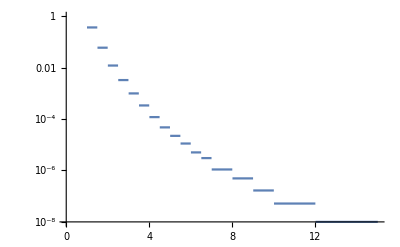

```mathematica
LogPlot[BinFunction[hep,pTbins][x],{x,0,15}]
```

```mathematica
Transpose[{Drop[pTbins,-1],hep}]
```

{{1.,{1.22,0.370.05}},{1.5,{1.72,0.0610.007}},{2.,{2.22,0.01220.0015}},{2.5,{2.73,0.00330.0004}},{3.,{3.23,0.001000.00013}},{3.5,{3.73,0.000340.00005}},{4.,{4.23,0.0001190.000015}},{4.5,{4.73,0.0000476}},{5.,{5.23,0.000022131}},{5.5,{5.74,0.000011116}},{6.,{6.24,5.00.710^-6}},{6.5,{6.74,3.00.510^-6}},{7.,{7.45,1.080.1810^-6}},{8.,{8.46,4.90.910^-7}},{9.,{9.46,1.60.410^-7}},{10.,{10.86,5.11.410^-8}},{12.,{13.25,10.4.10^-9}}}

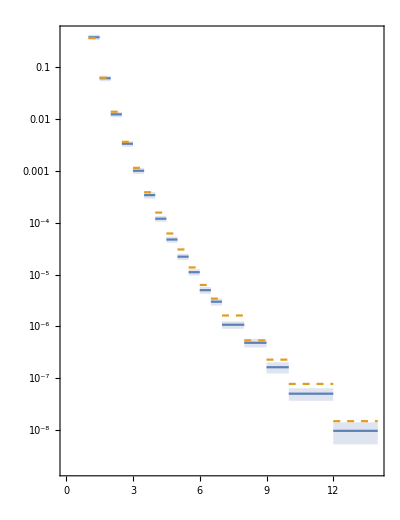

```mathematica
ListStepPlot[{Transpose[{Drop[pTbins,-1],hep[[All,2]]}],Transpose[{Drop[pTbins,-1],pythia[[All,2]]}],Transpose[{Drop[pTbins,-1],(Min@*Interval)/@hep[[All,2]]}],Transpose[{Drop[pTbins,-1],(Max@*Interval)/@hep[[All,2]]}]},Right,PlotRange->{{0,14},All},IntervalMarkers->None,Evaluate@style,PlotLegends->Placed[MaTeX/@{"\\text{PHENIX}","\\textsc{Pythia}"},{0.8,0.8}],FrameLabel->MaTeX/@{"p_T \\ [\\mathrm{GeV}]","\\mathrm{d}\\sigma/\\mathrm{d}p"},PlotMarkers->None,AspectRatio->1.3,Joined->False,ScalingFunctions->"Log",PlotStyle->{colors[[1]],{Dashed,colors[[2]]},None,None},Filling->{3->{4}},FillingStyle->Opacity[0.2,colors[[1]]]]
```

```mathematica
hepData=Import["HEP_phenix/Table1.csv"];
pT1=hepData[[All,1]];
σ1raw=hepData[[All,4]];
staterr=Interpreter["Percent"][#]&/@hepData[[All,5]];
syserr=Interpreter["Percent"][#]&/@hepData[[All,7]];
normerr=Interpreter["Percent"][#]&/@hepData[[All,9]];
hepError=√(staterr^2+syserr^2+normerr^2)//UnitConvert;
σ1=Around[#1,Scaled[#2]]&@@@Transpose[{σ1raw,hepError}];
hep=Transpose[{pT1,σ1}];

pythiaData=Import["Pythia/Tests/pT cross section/pT.csv"];
{pT2,σ2}=Transpose[{#1,Around[#2,#3]}&@@@pythiaData];
pythia=Transpose[{pT2,σ2}];
```

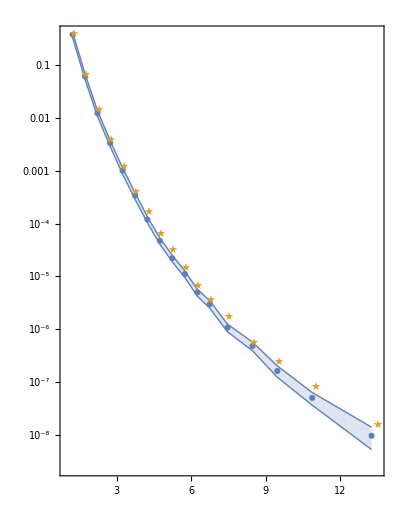

```mathematica
pTplot=ListLogPlot[{hep,pythia},PlotRange->All,IntervalMarkers->{"Bands",None},Evaluate@style,PlotLegends->Placed[MaTeX/@{"\\text{PHENIX}","\\textsc{Pythia}"},{0.8,0.8}],FrameLabel->MaTeX/@{"p_T \\ [\\mathrm{GeV}]","\\mathrm{d}\\sigma/\\mathrm{d}p"},PlotMarkers->{Automatic,"★"},AspectRatio->1.3]
```

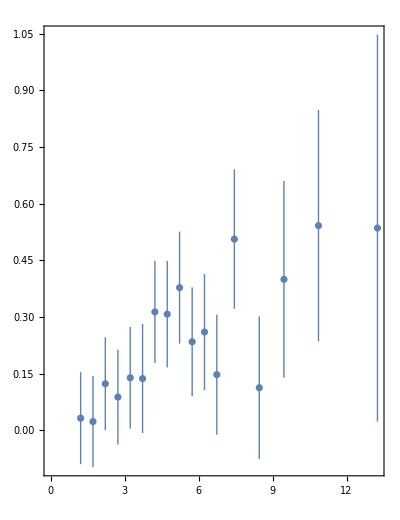

```mathematica
pTerror=ListPlot[Transpose[{pT1,Abs[σ1-(#["Value"]&/@σ2)]/σ1}],IntervalMarkers->"Bars",Evaluate@style,FrameLabel->MaTeX/@{"p_T \\ [\\mathrm{GeV}]","\\text{relative error}"},AspectRatio->1.3]
```

```mathematica
Export["Thesis/Graphics/pTplot.pdf",pTplot]
Export["Thesis/Graphics/pTerror.pdf",pTerror]
```

Thesis/Graphics/pTplot.pdf

Thesis/Graphics/pTerror.pdf

```mathematica
pTNoneData=Import["Pythia/Tests/pT cross section/pT_raw.csv"];
{pTNone,σNone}=Transpose[{#1,Around[#2,#3]}&@@@pTNoneData];
pTcsNone=Transpose[{pTNone,σNone}];
```

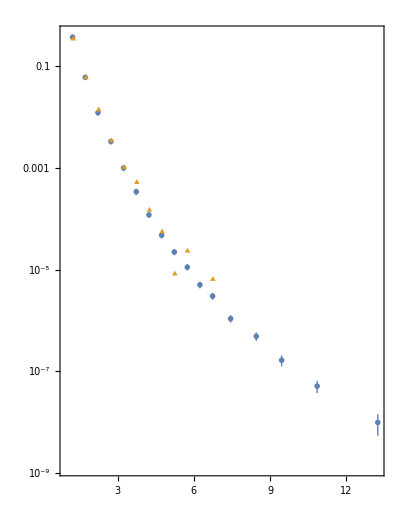

```mathematica
pTPlot1=ListLogPlot[{hep,pTcsNone},PlotRange->All,IntervalMarkers->{"Bars",None},Evaluate@style,PlotMarkers->{{Automatic,0.04},{Graphics[SSSTriangle[1,1,1]],0.03}},AspectRatio->1.3,PlotLabel->MaTeX["\\text{No bias or subdivision}"]]
```

```mathematica
pTBiasData=Import["Pythia/Tests/pT cross section/pT_bias.csv"];
{pTBias,σBias}=Transpose[{#1,Around[#2,#3]}&@@@pTBiasData];
pTcsBias=Transpose[{pTBias,σBias}];
```

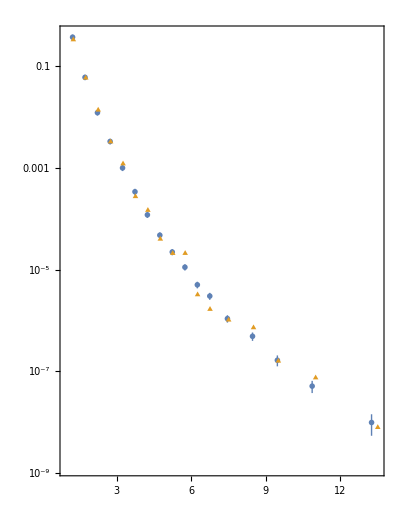

```mathematica
pTPlot2=ListLogPlot[{hep,pTcsBias},PlotRange->All,IntervalMarkers->{"Bars",None},Evaluate@style,PlotMarkers->{{Automatic,0.04},{Graphics[SSSTriangle[1,1,1]],0.03}},AspectRatio->1.3,PlotLabel->MaTeX["\\text{Bias, no subdivision}"]]
```

```mathematica
pTBiasSubdivisionData=Import["Pythia/Tests/pT cross section/pT_bias_subdivision.csv"];
{pTBiasSubdivision,σBiasSubdivision}=Transpose[{#1,Around[#2,#3]}&@@@pTBiasSubdivisionData];
pTcsBiasSubdivision=Transpose[{pTBiasSubdivision,σBiasSubdivision}];
```

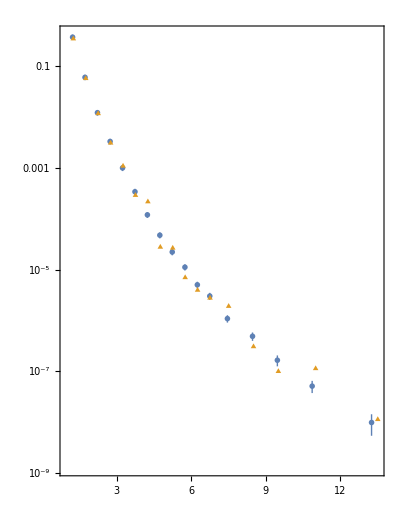

```mathematica
pTPlot3=ListLogPlot[{hep,pTcsBiasSubdivision},PlotRange->All,IntervalMarkers->{"Bars",None},Evaluate@style,PlotMarkers->{{Automatic,0.04},{Graphics[SSSTriangle[1,1,1]],0.03}},AspectRatio->1.3,PlotLegends->Placed[MaTeX/@{"\\textsc{Pythia}","\\text{PHENIX}"},Bottom],PlotLabel->MaTeX["\\text{Bias and subdivision}"]]
```

```mathematica
pTSubdivisionData=Import["Pythia/Tests/pT cross section/pT_bias_subdivision.csv"];
{pTSubdivision,σSubdivision}=Transpose[{#1,Around[#2,#3]}&@@@pTSubdivisionData];
pTcsSubdivision=Transpose[{pTSubdivision,σSubdivision}];
```

```mathematica
pTPlot4=ListLogPlot[{hep,pTcsSubdivision},PlotRange->All,IntervalMarkers->{"Bars",None},Evaluate@style,PlotMarkers->{{Automatic,0.04},{Graphics[SSSTriangle[1,1,1]],0.03}},AspectRatio->1.3,PlotLabel->MaTeX["\\text{No bias, subdivision}"]]
```

-Graphics-

```mathematica
pTplotIntermediate=PlotGrid[
{{pTPlot1,pTPlot2},
{pTPlot4,pTPlot3}},
FrameLabel->MaTeX/@{"p_T \\ [\\mathrm{GeV}]","\\mathrm{d}\\sigma/\\mathrm{d}p"},ImageSize->400,Spacings->{None,50}]
```

-Graphics-

```mathematica
Export["Thesis/Graphics/pTintermediate.pdf",pTplotIntermediate]
```

Thesis/Graphics/pTintermediate.pdf

```mathematica
pT5data1=Import["Pythia/Tests/pT cross section/pT5_1.csv"]
pT5data2=Import["Pythia/Tests/pT cross section/pT5_2.csv"];
pT5data3=Import["Pythia/Tests/pT cross section/pT5_3.csv"];
pT5data4=Import["Pythia/Tests/pT cross section/pT5_4.csv"];
```

```mathematica
pT6data1=Import["Pythia/Tests/pT cross section/pT6_1.csv"];
pT6data2=Import["Pythia/Tests/pT cross section/pT6_2.csv"];
pT6data3=Import["Pythia/Tests/pT cross section/pT6_3.csv"];
pT6data4=Import["Pythia/Tests/pT cross section/pT6_4.csv"];
```

```mathematica
HistogramMean[list_]:=Transpose[{list[[1,All,1]],MeanAround/@Transpose[list[[All,All,2]]]}]
```

```mathematica
RelativeError[x_?NumericQ]:=x
RelativeError[around_]:=around["Uncertainty"]/around["Value"]/;Head[around]==Around
```

```mathematica
pTmean1=HistogramMean[{pT5data1,pT5data2,pT5data3,pT5data4}]
pTmean2=HistogramMean[{pT6data1,pT6data2,pT6data3,pT6data4}];
```

(1.25 | 0.35760.0022
1.75 | 0.05990.0016
2.25 | 0.01320.0007
2.75 | 0.00320.0004
3.25 | 0.001020.00017
3.75 | 0.0003210.000033
4.25 | 0.0001010.000019
4.75 | 0.0000500.000015
5.25 | 0.000015324
5.75 | 0.00001005
6.25 | 8.12.710^-6
6.75 | 2.70.710^-6
7.5 | 1.270.1910^-6
8.5 | 4.50.810^-7
9.5 | 1.760.1810^-7
11 | 6.10.910^-8
13.5 | 1.560.2310^-8)

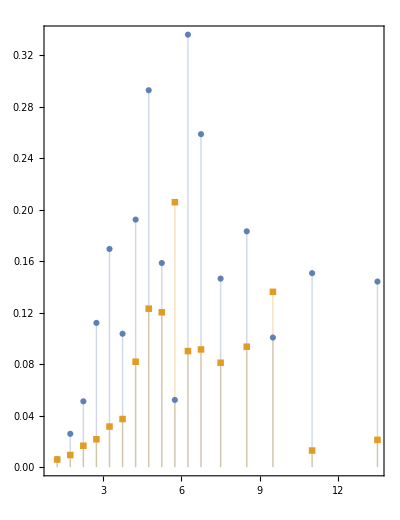

```mathematica
pTmeanError=ListPlot[{Map[RelativeError,pTmean1,{2}],Map[RelativeError,pTmean2,{2}]},PlotRange->All,Evaluate@style,AspectRatio->1.3,Filling->Bottom,FrameLabel->MaTeX/@{"p_T \\ [\\mathrm{GeV}]","\\text{relative error}"},PlotLegends->MaTeX/@{"N=10^5","N=10^6"},PlotMarkers->Automatic]
```